```mathematica
(*There are 30 words, extract 5 each time,then put them back. The question is the distribution of the times when every word has been extracted for at least one time*)
```

```mathematica
For[i=1,i≤40,i++,
For[j=0,j≤30,j++,
   a[i,j]=0]];
a[1,5]=1;
a[2,5]=1/Binomial[30,5]//N;
a[2,6]=(Binomial[25,1]*Binomial[5,4])/Binomial[30,5]//N;
a[2,7]=(Binomial[25,2]*Binomial[5,3])/Binomial[30,5]//N;
a[2,8]=(Binomial[25,3]*Binomial[5,2])/Binomial[30,5]//N;
a[2,9]=(Binomial[25,4]*Binomial[5,1])/Binomial[30,5]//N;
a[2,10]=Binomial[25,5]/Binomial[30,5]//N;
```

```mathematica
For[m=3,m≤40,m++,
For[n=5,n≤30,n++,a[m,n]=(a[m-1,n-5]*Binomial[35-n,5]+a[m-1,n-4]*Binomial[34-n,4]*Binomial[n-4,1]+a[m-1,n-3]*Binomial[33-n,3]*Binomial[n-3,2]+a[m-1,n-2]*Binomial[32-n,2]*Binomial[n-2,3]+
a[m-1,n-1]*Binomial[31-n,1]*Binomial[n-1,4]+
a[m-1,n]*Binomial[n,5])/Binomial[30,5]//N]]
```

```mathematica
list={};
```

```mathematica
For[i=6,i≤40,i++,AppendTo[list,a[i,30]]]
```

```mathematica
list2=Range[6,40];
```

```mathematica
list3={list2,list};
```

```mathematica
list3=Transpose[list3];
```

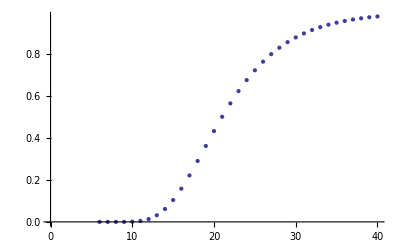

```mathematica
ListPlot[list3]
```

```mathematica
(*from the figure above we can see that even the process is repeated for 30 times. the probability that every word has been extracted for at least one time is not larger than 95 percent.Up to this point, each word is repeated about 5 times*)
```